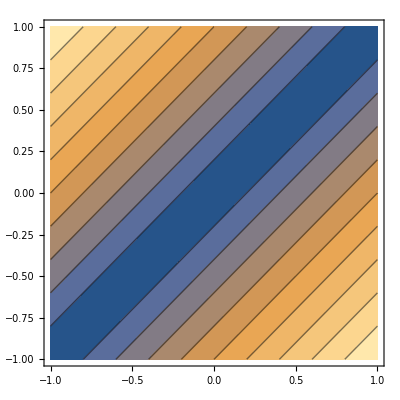

```mathematica
ContourPlot[Abs[x-y], {x, -1, 1}, {y, -1, 1}]
```

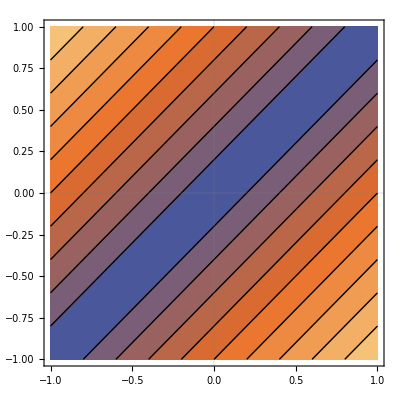

```mathematica
ContourPlot[Abs[x-y],{x,-1,1},{y,-1,1},PlotTheme->"Scientific"]
```

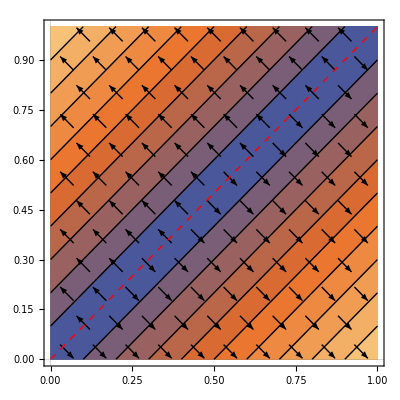

```mathematica
F[x_,y_]= Abs[x-y];
Show[
ContourPlot[F[x, y], {x, 0, 1}, {y, 0, 1}, PlotTheme->"Scientific"],VectorPlot[If[x- y < 0, {-1, 1}, {1, -1}], {x,0, 1}, {y,0,1}, PlotTheme->"Monochrome",
VectorSizes->Small,
VectorPoints->Coarse],
Graphics[{Thick, Red,Dashed,Line[{{0,0}, {1,1}}]}]]
```

If[Abs[x-y]<0.5,{Dx[x,y],Dy[x,y]},{0,0}]

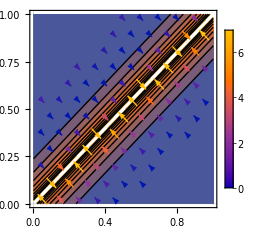

```mathematica
B[x_,y_]=-(x-y-.5)^2 Log[x-y];
Dx [x_,y_]= D[B[x,y],x];
Dy [x_,y_]= D[B[x,y],y];
V[x_,y_]=If[Abs[x-y] < .5,{Dx[x,y], Dy[x,y]},{0,0}] 
Show[
ContourPlot[
If[x>y,B[x,y],B[1-x,1-y]] ,{x, 0, 1}, {y, 0,1},
PlotTheme->"Scientific"],VectorPlot[
V[x,y] ,{x, 0, 1}, {y, 0,1},
VectorScaling->"Linear",
VectorPoints->Coarse,
PlotLegends->Automatic]]
```

```mathematica
Export["/Users/yangjerry/Desktop/Untitled.png",%50,"PNG"]
```

/Users/yangjerry/Desktop/Untitled.png